{1,1,1,1,1,1,3,1,1,1,1,1,1}

The Magenta points are the original data points. The pink points are on the curve and they are setted by the parameters, ti. The red points are also on the curve and they are set by knots. They seperate the curve to L segment. The gray lines link the control points after iteration. The blue lines link the final control points. The magenta curve shows the curve after first iteration and the green curve is the final curve.

-Graphics3D-

-Graphics-

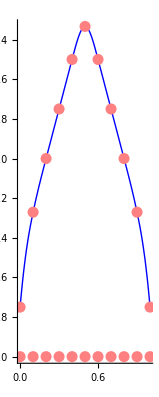

```mathematica
data1=Table[{Cos[x]//N, Sin[x]//N,1},{x,0,6}];
data2=Table[{x, Sin[x]//N,1},{x,0,12}];


pts=data1;
l=Length[pts];

wts={1,1,1,3,1,1,1};


wtsfun2[len_]:=Join[Table[1,{i,Floor[len/2]}],{3},Table[1,Floor[len/2]]];
wtsfun1[len_]:=Join[Table[i,{i,Ceiling[len/2]}],Table[Ceiling[len/2]-i,{i,Floor[len/2]}]];
wtsfun[len_]:=Table[Binomial[len-1,k],{k,0,len}];
wts=wtsfun2[Length[pts]]
(*chord length parameter*)
(*calculate the distance for parameter*)
dist[pts_]:=Accumulate[Table[EuclideanDistance[pts[[i]],pts[[i+1]]],{i,Length[pts]-1}]];
(*set ti from 0 to 1 by using Chord length*)
uparam[pts_]:=N[Prepend[dist[pts]/Last[dist[pts]],0]];

(*I used the two function to calculate the knots first. The result is almost the same, so I used uniformed knots.*)
(*set ti for different control points*)
ctrlparam[n_,pts_,param_]:=Join[Table[0,{i,0,0}],Table[Sum[param[[i]],{i,j,Length[pts]-n+j}]/(Length[pts]-n+1),{j,2,n-1}],Table[1,{i,0,0}]];
(*set knot for different degree*)
kfun[d_,ctrlparam_]:=Join[Table[0,{i,0,d}],Table[Sum[ctrlparam[[i]],{i,j,j+d-1}]/d,{j,2,Length[ctrlparam]-d}], Table[1,{i,0,d}]];

knotfun[l_,uparam_]:=Join[Table[0,{i,0,3}],Table[(uparam[[Ceiling[i*Length[uparam]/l]]]+uparam[[Floor[i*Length[uparam]/l]]])/2,{i,1,l-1}],Table[1,{i,0,3}]];

(*calculate the basis*)
(*Built the matrix M for least square*)
mbasis[uparam_,n_,d_,knot_]:=With[{param=uparam},Table[BSplineBasis[{d,knot},j-1,param[[i]]],{i,Length[param]},{j,n}]];
bzcurve[pts_,knot_,n_,d_,t_]:=Sum[BSplineBasis[{d,knot},i,t]*pts[[i+1]],{i,0,(Length[pts]-1)}];
curve[pts_,knot_,n_,d_,t_]:=Sum[BSplineBasis[{d,knot},i,t]*pts[[i+1]]*wts[[i+1]],{i,0,(Length[pts]-1)}]/Sum[BSplineBasis[{d,knot},i,t]*wts[[i+1]],{i,0,(Length[pts]-1)}];
wtfuncurve[pts_,knot_,n_,d_,t_]:=Sum[BSplineBasis[{d,knot},i,t]*wts[[i+1]],{i,0,(Length[pts]-1)}];
curve3D[pts_,knot_,n_,d_,t_]:=Sum[BSplineBasis[{d,knot},i,t]*pts[[i+1]]*wts[[i+1]],{i,0,(Length[pts]-1)}];

Print[Style["The Magenta points are the original data points. The pink points are on the curve and they are setted by the parameters, ti. The red points are also on the curve and they are set by knots. They seperate the curve to L segment. The gray lines link the control points after iteration. The blue lines link the final control points. The magenta curve shows the curve after first iteration and the green curve is the final curve.",18,Red]];


n=l+3;
d=3;

(*Original parameter.*)
param=uparam[pts];
(*(*For different amount of control points, set different parameter.*)
ctrlparameter=ctrlparam[n,pts,param];*)
(*The knots for different degree*)

knot=Join[ConstantArray[0,d],Range[0,1,1/(n-d)],ConstantArray[1,d]];
(*knot=knotfun[l,param]*)
(*The control point*)
ctrlpts=LeastSquares[mbasis[param,n,d,knot],pts];
mbasis[param,n,d,knot];

crtparam=param;
(*crtctrlparameter=ctrlparameter;*)
crtknot=knot;
crtctrlpts=ctrlpts;
(*use this funtion to get the vector on curve*)
divcurve[t_]:=curve[crtctrlpts,crtknot,n,d,t];

(*The length of the curve.*)
curvelength=ArcLength[curve[crtctrlpts,crtknot,n,d,t],{t,crtknot[[d+1]],knot[[Length[crtknot]-d]]}];

(*error represent the distance between original data points with the points on the curve which set by parameter ti.*)
error=Table[0,{j,1,Length[pts]}];
(*The vector at ti on the curve*)
tengentvec=Table[{0,0},{j,1,Length[pts]}];
(*The vecter from points on curve to data points*)
errvec=Table[{0,0},{j,1,Length[pts]}];
(*The angle between two vecter*)
vecang=Table[0,{j,1,Length[pts]}];
(*The length used to change ti*)
lengthl=Table[0,{j,1,Length[pts]}];
error1=error;
vecang1=vecang;
crtctrlpts1=crtctrlpts;

(*Do[(
Do[
error[[j]]=EuclideanDistance[curve[crtctrlpts,crtknot,n,d,crtparam[[j]]],pts[[j]]];
tengentvec[[j]]=divcurve'[crtparam[[j]]];
errvec[[j]]=pts[[j]]-curve[crtctrlpts,crtknot,n,d,crtparam[[j]]];
If[error[[j]]==0,vecang[[j]]=0,vecang[[j]]=VectorAngle[tengentvec[[j]],errvec[[j]]]];
lengthl[[j]]=error[[j]]*Cos[vecang[[j]]];
(*Parameter correction. If the length of new vector is less than the original vector, do the correction, else the ti will be corrected by half of the length.*)
tmplengthl=lengthl[[j]];
tmpparam=crtparam[[j]];
If[crtparam[[j]]+tmplengthl>1,tmpparam=1,If[crtparam[[j]]+tmplengthl<0,tmpparam=0,tmpparam=crtparam[[j]]+tmplengthl;]];
While[EuclideanDistance[curve[crtctrlpts,crtknot,n,d,tmpparam],pts[[j]]]>error[[j]]&&tmplengthl≠0,(tmplengthl=tmplengthl/2;If[crtparam[[j]]+tmplengthl>1,tmpparam=1,If[crtparam[[j]]+tmplengthl<0,tmpparam=0,tmpparam=crtparam[[j]]+tmplengthl;]];)];
If[tmpparam<0,crtparam[[j]]=0,If[tmpparam>1,crtparam[[j]]=1,crtparam[[j]]=tmpparam;]];
,{j,1,Length[pts]}];
(*Here is the control points after correction*)
crtctrlpts=LeastSquares[mbasis[crtparam,n,d,crtknot],pts];
(*store the data after first iteration*)
If[k==1,
(error1=error;
vecang1=vecang;
crtctrlpts1=crtctrlpts;
crtparam1=crtparam;)];

)
,{k,1,iter}];*)

(*(*get the max, min, mean error and angle*)
errmax1=Max[error1];
errmin1=Min[error1];
errave1=Mean[error1];
errmax=Max[error];
errmin=Min[error];
errave=Mean[error];
angmax1=Max[vecang1];
angmin1=Min[vecang1];
angave1=Mean[vecang1];
angmax=Max[vecang];
angmin=Min[vecang];
angave=Mean[vecang];
*)

(*Output the curves, points and polygon*)
datapts=Graphics3D[{Magenta,PointSize[0.015],Point[pts],PointSize[0.02],Point[pts[[1]]]}];
jpts = Table[curve[crtctrlpts,crtknot,n,d,crtknot[[i]]], {i,d+1,Length[crtknot]- d,1}];
jptsplot = Graphics3D[{Red,PointSize[0.015],Point[jpts]}];

parpts=Table[curve[crtctrlpts,crtknot,n,d,crtparam[[j]]],{j,1,Length[pts]}];
parptsplot=Graphics3D[{Pink,PointSize[0.02],Point[parpts]}];
ctrlpoints=Graphics3D[{Black,PointSize[0.02],Point[crtctrlpts]}];

cplot=ParametricPlot3D[curve[crtctrlpts,crtknot,n,d,t],{t,crtknot[[d+1]],crtknot[[Length[crtknot]-d]]},PlotStyle->{Thick,Green}];
bzcplot=ParametricPlot3D[bzcurve[crtctrlpts,crtknot,n,d,t],{t,crtknot[[d+1]],crtknot[[Length[crtknot]-d]]},PlotStyle->{Thick,Blue}];
cplot1=ParametricPlot3D[curve[crtctrlpts1,crtknot,n,d,t],{t,crtknot[[d+1]],crtknot[[Length[crtknot]-d]]},PlotStyle->{Thick,Magenta}];
cplot3D=ParametricPlot3D[curve3D[crtctrlpts,crtknot,n,d,t],{t,crtknot[[d+1]],crtknot[[Length[crtknot]-d]]},PlotStyle->{Thick,Red}];

ddplot=Graphics3D[{Line[crtctrlpts,VertexColors->Blue]}];
ddplot1=Graphics3D[{Line[crtctrlpts1,VertexColors->Gray]}];

wtfunplot=ParametricPlot[{t,wtfuncurve[crtctrlpts,crtknot,n,d,t]},{t,crtknot[[d+1]],crtknot[[Length[crtknot]-d]]},PlotStyle->{Thick,Blue}];
wtfpts=Table[{crtknot[[i]],wtfuncurve[crtctrlpts,crtknot,n,d,crtknot[[i]]]}, {i,d+1,Length[crtknot]- d,1}];
wtfpts1=Table[{crtknot[[i]],0}, {i,d+1,Length[crtknot]- d,1}];
wtfpoints=Graphics[{Pink,PointSize[0.05],Point[wtfpts]}];
wtfpoints1=Graphics[{Pink,PointSize[0.05],Point[wtfpts1]}];
Show[{cplot1,ctrlpoints,bzcplot,datapts,ddplot,ddplot1,cplot,jptsplot},Axes->True,PlotRange->All,ImageSize->400]
Show[{wtfpoints1,wtfunplot,wtfpoints},Axes->True]
```